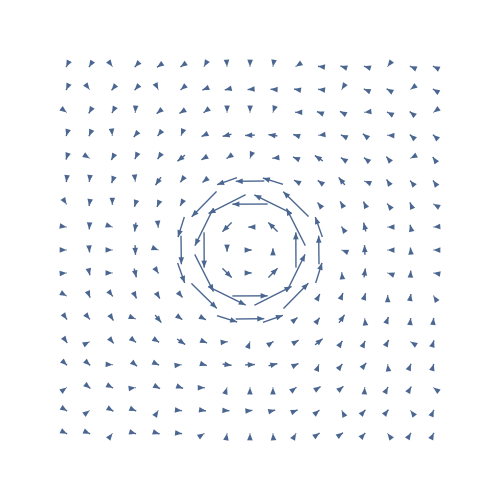

```mathematica
λ=632.8;
ϵr=-15.847+1.076 *I;
kx=(2Pi)/λ*√(ϵr/(ϵr+1));kz=-(2Pi)/λ*√(1/(ϵr+1));k0=2Pi/λ;
a=1/Im[kx];λspp=2Pi/Re[kx];
ρ=√(x^2+y^2)*λ;
S1=Re[I*Sum[BesselJ[n,kx*ρ]*Conjugate[BesselJ[n-1,kx*ρ]-BesselJ[n+1,kx*ρ]],{n,3,3}]];
S2=Re[Sum[BesselJ[n,kx*ρ]*Conjugate[BesselJ[n-1,kx*ρ]+BesselJ[n+1,kx*ρ]],{n,3,3}]];
VectorPlot[{S1*x/(√(x^2+y^2))-S2*y/(√(x^2+y^2)),S1*y/(√(x^2+y^2))+S2*x/(√(x^2+y^2))},{x,-2,2},{y,-2,2},VectorScale->0.08,VectorPoints->17,ImageSize->500,PlotRangePadding->None,Frame->False]
```

Simulation of the SPPV field. The average OAM are 0, 4, 6, -6 for three modes fields. 
   
OAM = 0, modes : -1, 0, 1;
OAM = 4, modes : 3, 4, 5;
OAM = 6, modes : 5, 6, 7;
OAM = -6, modes : -7, -6, -5;

Second simulation. The OAM = 3, the mode number =  1, 5, 9, 15.
For the m.n. = 1, the modes : = 3
For the m.n. = 5, the modes : = 1, 2, 3, 4, 5.
For the m.n. = 9, the modes : = -1 t0 7.
For the m.n. = 15, the modes : = -4 to 10. 

The figures includs the energy density and the Ponting vector.